```mathematica
SetDirectory[NotebookDirectory[]];
Nc=3.;
mf2[h_,ρ_]:=(h^2 ρ)/2;
nff[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)-μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)-μ)/T]+1)];
nfa[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)+μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)+μ)/T]+1)];
F1[q_,ρ_,h_,T_,μ_]:=q^2/(2 √(q^2+mf2[h,ρ]))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]);
F1F1m[q_,p0_,ps_,x_,ρ_,h_,T_,μ_]:=q^2/(4 √(q^2+mf2[h,ρ])√((q^2+ps^2-2q ps x)+mf2[h,ρ]))((nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]+nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]-nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nff[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ])));
gamma2thr[p0_,ps_,ρ_,h_,T_,μ_]:=-(h^2 Nc)/(2π)^2 NIntegrate[(2F1[q,ρ,h,T,μ]-(p0^2+ps^2)F1F1m[q,p0,ps,x,ρ,h,T,μ]),{q,0.,500.,5000.},{x,-1,1},AccuracyGoal->5,PrecisionGoal->5,
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->6];
(*gammavac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]+(p0^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5])-(Nc h^2 mf2[h,ρ])/(16 π^2);*)
(*gammavac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]+(p0^2+ps^2)/2*(-2+Log[mf2[h,ρ]/MZ^2]+(√(4 mf2[h,ρ]+(p0^2+ps^2)) Log[((√(p0^2+ps^2))+√(4 mf2[h,ρ]+(p0^2+ps^2)^2))/(-(√(p0^2+ps^2))+√(4 mf2[h,ρ]+(p0^2+ps^2)^2))])/(√(p0^2+ps^2))))-(Nc h^2 mf2[h,ρ])/(16 π^2);*)
gammavac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((p0^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->50]);
gamma2[p0_,ps_,ρ_,h_,T_,μ_,Mmass_,MZ_]:=gamma2thr[p0,ps,ρ,h,T,μ]+gammavac[p0,ps,ρ,h,Mmass,MZ];
λ300=75.8;
ν300=-482.^2;
```

## finite T data μ=0

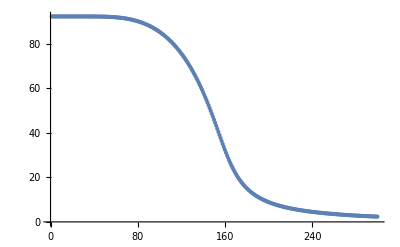

```mathematica
fpi=Flatten[Transpose[Import["./M300.dat"]]];
fpimu0=fpi[[1;;300]];
ListPlot[fpimu0]
```

```mathematica
T=Table[10+(i-1)*5,{i,1,49}]
```

{10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250}

```mathematica
sigmamu0T=Table[ParallelTable[gamma2[0.,p,fpimu0[[10+(i-1)*5]]^2/2,6.5,10+(i-1)*5,0.,300.,300.]+(p)^2+(λ300 fpimu0[[10+(i-1)*5]]^2/2+ν300)//Quiet,{p,1,800,20}],{i,1,49}];
```

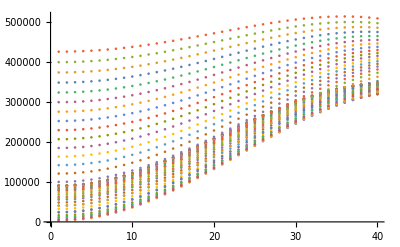

```mathematica
ListPlot[sigmamu0T]
```

```mathematica
Table[Export["./sigmapi_mu0_T/sigmaT"<>ToString[10+(i-1)*5]<>".dat",Re[sigmamu0T][[i]]],{i,1,49}];
```

## finite mu data T=50 MeV

{5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305,310,315,320,325,330,335,340,345,350,355,360,365,370,375,380,385,390,395,400,405,410,415,420,425,430,435,440,445,450,455,460,465,470,475,480,485,490,495,500}

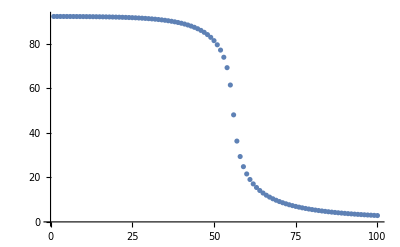

```mathematica
fpimu=Flatten[Transpose[Import["./sigmaT50_mu.dat"]]];
mu=Flatten[Import["./mu5to500.dat"]]
ListPlot[fpimu]
```

```mathematica
mu[[20]]
```

100

```mathematica
Length[mu]
```

100

```mathematica
Length[Table[i,{i,1,800,20}]]
```

40

```mathematica
Table[i,{i,1,800,20}]
```

{1,21,41,61,81,101,121,141,161,181,201,221,241,261,281,301,321,341,361,381,401,421,441,461,481,501,521,541,561,581,601,621,641,661,681,701,721,741,761,781}

```mathematica
sigmaT50mu=Table[ParallelTable[gamma2[0.,p,fpimu[[i]]^2/2,6.5,50.,mu[[i]],300.,300.]+(p)^2+(λ300 fpimu[[i]]^2/2+ν300)//Quiet,{p,1,800,20}],{i,20,100}];
```

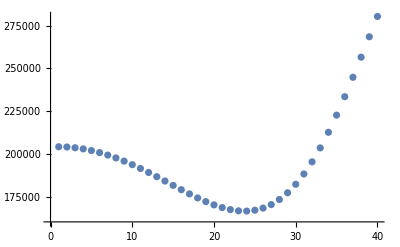

```mathematica
ListPlot[sigmaT50mu[[53]]]
```

```mathematica
Table[Export["./sigmapi_mu_T50/sigmamu"<>ToString[100+(i-1)*5]<>".dat",Re[sigmaT50mu][[i]]],{i,1,81}];
```

## M values

```mathematica
fixM1=ParallelTable[gamma2[0.,p,(sigmadata[[64]][[30]])^2/2,6.5,30.,320.,√(300.^2),√(300.^2)]+(p)^2+(λ300 (sigmadata[[64]][[30]])^2/2+ν300),{p,1,1000,10}];
```

$Aborted

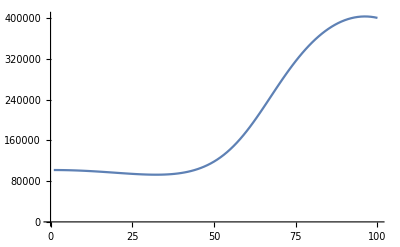

```mathematica
ListLinePlot[fixM1]
```

```mathematica
Mp=ParallelTable[gamma2[0.,p,(sigmadata[[64]][[30]])^2/2,6.5,30.,320.,√(300.^2),√(300.^2+(p^2))]+(p)^2+(λ300 (sigmadata[[64]][[30]])^2/2+ν300),{p,1,1000,10}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Mp2=ParallelTable[gamma2[0.,p,(sigmadata[[64]][[30]])^2/2,6.5,30.,320.,√(300.^2),√(300.^2+(2 p^2))]+(p)^2+(λ300 (sigmadata[[64]][[30]])^2/2+ν300),{p,1,1000,10}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ps=Table[i*10,{i,1,100}];
```

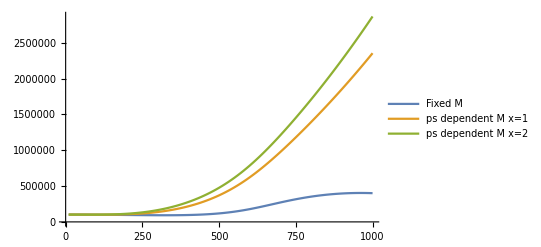

```mathematica
ListLinePlot[{Transpose[{ps,fixM}],Transpose[{ps,Mp}],Transpose[{ps,Mp2}]},PlotLegends->{"Fixed M","ps dependent M x=1","ps dependent M x=2"}]
```

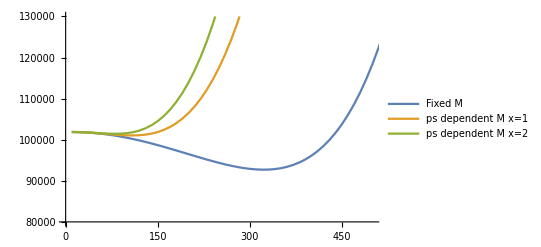

```mathematica
ListLinePlot[{Transpose[{ps,fixM}],Transpose[{ps,Mp}],Transpose[{ps,Mp2}]},PlotRange->{{0,500},{80000,130000}},PlotLegends->{"Fixed M","ps dependent M x=1","ps dependent M x=2"}]
```

## High T (CA effect)

```mathematica
T300mu0=ParallelTable[gamma2[0.,p,(sigmadata[[1]][[300]])^2/2,6.5,300.,0.,√(300.^2),√(300.^2)]+(p)^2+(λ300 (sigmadata[[1]][[300]])^2/2+ν300),{p,1,1000,10}];
```

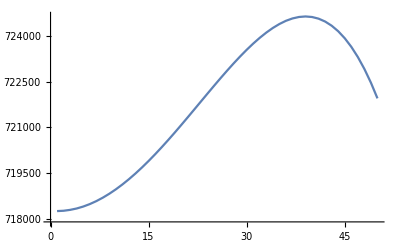

```mathematica
ListLinePlot[T300mu0[[1;;50]]]
```